```mathematica
TableForm[Sort[AllTrianglesWithPattern[6],PartitionCompare],TableDepth->2]
```

{1,3} | {2,4} | {5} | {6}
{1,3} | {2,5} | {4} | {6}
{1,4} | {2,5} | {3} | {6}
{1,4} | {2} | {3,5} | {6}
{1} | {2,4} | {3,5} | {6}

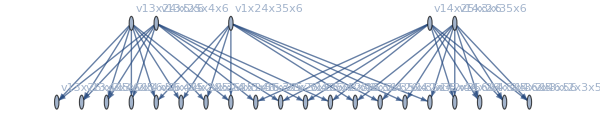
{8,2,2,2,2,2,2,2,2,8,2,2,2,2,2,2,2,2,8,2,2,2,2,8,8}
-Graphics-

```mathematica
Column[With[{g=Graph[
Flatten[With[{max=6},
Table[
If[MeetDistance[t,q]==1,
SetsToSymbol[t]->SetsToSymbol[q],{}],
{t,AllTrianglesWithPattern[max]},
{q,AllQuadrilateralsWithPattern[max]}
]
]],GraphLayout->"LayeredDigraphEmbedding", VertexLabels->"Name",ImageSize->600]},
{Table[VertexDegree[g,v],{v,VertexList[g]}],
g}
]
]
```

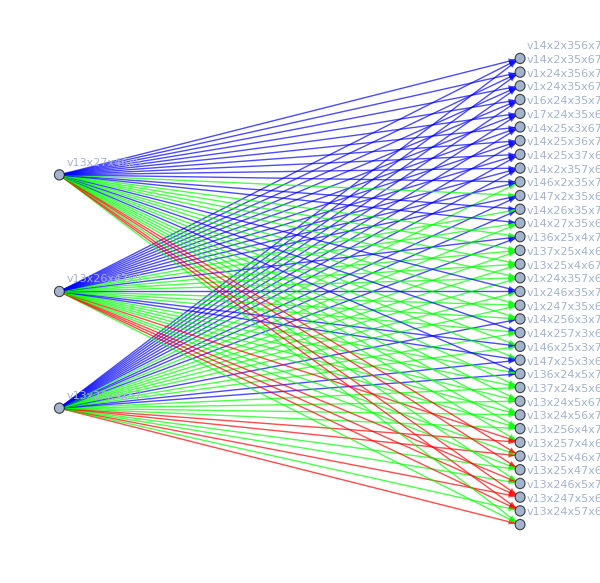

```mathematica
Block[{max=7,edges=Association[],all},
Table[
edges[dist]=Flatten[Table[
If[MeetDistance[t,q]==dist,
SetsToSymbol[q]->SetsToSymbol[t],{}],
{t,AllTrianglesWithPattern[max]},
{q,Take[AllQuadrilateralsWithPattern[max],3]}
]],
{dist,1,max-4}
];
all=Flatten[Join[Table[edges[dist],{dist,1,max-4}]]];
Graph[all,EdgeStyle->Flatten[Table[Map[#->{Red,Green,Blue}[[dist]]&,edges[dist]],{dist,1,max-4}]],
GraphLayout->"BipartiteEmbedding", VertexLabels->"Name",ImageSize->600]
]
```

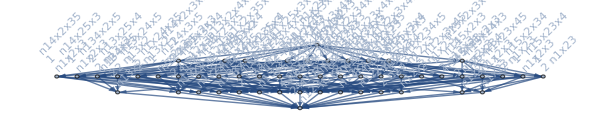

```mathematica
MobiusGraph4[K5Key,allGraphs5]
```

```mathematica
Incoming[part_]:=Sum[StirlingS2[Length[p],2],{p,part}]
```

```mathematica
Table[Incoming[SymbolToSets[allGraphs5[k,"colofour"]]],{k,allGraphs5AtomKeys}]
```

{0,1,1,1,3,1,2,1,2,3,1,2,3,3,7,1,2,2,2,4,1,2,2,2,4,3,4,1,2,2,2,4,3,4,3,4,7,1,2,2,2,4,3,4,3,4,7,3,4,7,7,15}

```mathematica
StirlingS2[5,2]
```

15

```mathematica
Rank[setp5]
```

{0,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4}

```mathematica
allCover=Block[{
set=setp8,
points=Association[],i, basePoints,result=Association[],sets},
basePoints=P[set];
For[i=1,i≤ Length[basePoints],i++,
sets=PointerToSets[basePoints[[i]]];
points[i]=sets;
result[sets]={}
];
Table[
AppendTo[result[points[cover[[2]]]],points[cover[[1]]]]
,
{cover,CoverRelations[set]}
];
result
];
```

```mathematica
AllTrianglesWithPattern[7]
```

{{{1,3},{2,4},{5,7},{6}},{{1,3},{2,4},{5,6},{7}},{{1,3},{2,4},{5},{6,7}},{{1,3,7},{2,4},{5},{6}},{{1,3,6},{2,4},{5},{7}},{{1,3},{2,4,7},{5},{6}},{{1,3},{2,4,6},{5},{7}},{{1,4},{2,5},{3,7},{6}},{{1,4},{2,5},{3,6},{7}},{{1,4},{2,5},{3},{6,7}},{{1,4,7},{2,5},{3},{6}},{{1,4,6},{2,5},{3},{7}},{{1,4},{2,5,7},{3},{6}},{{1,4},{2,5,6},{3},{7}},{{1,7},{2,4},{3,5},{6}},{{1,6},{2,4},{3,5},{7}},{{1},{2,4},{3,5},{6,7}},{{1},{2,4,7},{3,5},{6}},{{1},{2,4,6},{3,5},{7}},{{1},{2,4},{3,5,7},{6}},{{1},{2,4},{3,5,6},{7}},{{1,3},{2,5},{4,7},{6}},{{1,3},{2,5},{4,6},{7}},{{1,3},{2,5},{4},{6,7}},{{1,3,7},{2,5},{4},{6}},{{1,3,6},{2,5},{4},{7}},{{1,3},{2,5,7},{4},{6}},{{1,3},{2,5,6},{4},{7}},{{1,4},{2,7},{3,5},{6}},{{1,4},{2,6},{3,5},{7}},{{1,4},{2},{3,5},{6,7}},{{1,4,7},{2},{3,5},{6}},{{1,4,6},{2},{3,5},{7}},{{1,4},{2},{3,5,7},{6}},{{1,4},{2},{3,5,6},{7}}}

```mathematica
allCover[{{1,3},{2,4},{5,7},{6}}]
```

Missing[KeyAbsent,{{1,3},{2,4},{5,7},{6}}]

```mathematica
WhichQuadrilateralPattern[{{1},{2,4},{3},{5,6,7}}]
```

5

```mathematica
colorMap={-1->Style[-1,Red],1->Style[1,Darker[Green]],2->Style[2,Blue],3->Style[3,Darker[Yellow]],4->Style[4,Orange],5->Style[5,Black]}
```

{-1→-1,1→1,2→2,3→3,4→4,5→5}

```mathematica
Table[
Map[WhichQuadrilateralPattern[#]&,allCover[t]]/.colorMap,{t,AllTrianglesWithPattern[8]}
]
```

{{-1,-1,2,5},{-1,-1,2,5},{-1,-1,2,5},{-1,2,-1,5,5},{-1,2,-1,5,5},{-1,2,-1,5,5},{-1,2,-1,5,5},{-1,2,-1,5,5},{-1,2,-1,5,5},{-1,2,-1,5,5},{-1,2,-1,5,5},{-1,2,-1,5,5},{-1,-1,2,2,5},{-1,-1,2,2,5},{-1,-1,2,2,5},{-1,-1,2,2,5},{-1,-1,2,2,5},{-1,-1,2,2,5},{-1,-1,2,2,5},{-1,-1,2,2,5},{-1,-1,2,2,5},{-1,-1,-1,2,5},{-1,-1,-1,2,5},{-1,-1,-1,2,5},{-1,-1,-1,2,5},{-1,2,2,-1,5,5},{-1,2,2,-1,5,5},{-1,2,2,-1,5,5},{-1,2,2,-1,5,5},{-1,2,2,-1,5,5},{-1,2,2,-1,5,5},{2,-1,-1,-1,5,5,5,5},{2,-1,-1,-1,5,5,5,5},{2,-1,-1,-1,5,5,5,5},{-1,-1,-1,2,2,2,2,5},{-1,-1,-1,2,2,2,2,5},{-1,-1,-1,2,2,2,2,5},{-1,-1,3,4},{-1,-1,3,4},{-1,-1,3,4},{-1,3,-1,4,4},{-1,3,-1,4,4},{-1,3,-1,4,4},{-1,3,-1,4,4},{-1,3,-1,4,4},{-1,3,-1,4,4},{-1,-1,3,3,4},{-1,-1,3,3,4},{-1,-1,3,3,4},{-1,-1,3,3,4},{-1,-1,3,3,4},{-1,-1,3,3,4},{-1,-1,-1,3,4},{-1,-1,-1,3,4},{-1,-1,-1,3,4},{-1,3,-1,4,4},{-1,3,-1,4,4},{-1,3,-1,4,4},{-1,-1,3,3,4},{-1,-1,3,3,4},{-1,-1,3,3,4},{-1,-1,-1,3,4},{-1,3,3,-1,4,4},{-1,3,3,-1,4,4},{-1,3,3,-1,4,4},{-1,3,3,-1,4,4},{-1,3,3,-1,4,4},{-1,3,3,-1,4,4},{3,-1,-1,-1,4,4,4,4},{3,-1,-1,-1,4,4,4,4},{3,-1,-1,-1,4,4,4,4},{-1,-1,-1,3,3,3,3,4},{-1,-1,-1,3,3,3,3,4},{-1,-1,-1,3,3,3,3,4},{-1,5,1,-1},{-1,5,1,-1},{-1,5,1,-1},{5,-1,1,1,-1},{5,-1,1,1,-1},{5,-1,1,1,-1},{5,-1,1,1,-1},{5,-1,1,1,-1},{5,-1,1,1,-1},{-1,5,5,1,-1},{-1,5,5,1,-1},{-1,5,5,1,-1},{-1,5,5,1,-1},{-1,5,5,1,-1},{-1,5,5,1,-1},{5,1,-1,-1,-1},{5,1,-1,-1,-1},{5,1,-1,-1,-1},{-1,5,-1,1,1},{-1,5,-1,1,1},{-1,5,-1,1,1},{-1,-1,5,5,1},{-1,-1,5,5,1},{-1,-1,5,5,1},{-1,-1,-1,5,1},{-1,5,5,-1,1,1},{-1,5,5,-1,1,1},{-1,5,5,-1,1,1},{-1,5,5,-1,1,1},{-1,5,5,-1,1,1},{-1,5,5,-1,1,1},{5,-1,-1,-1,1,1,1,1},{5,-1,-1,-1,1,1,1,1},{5,-1,-1,-1,1,1,1,1},{-1,-1,-1,5,5,5,5,1},{-1,-1,-1,5,5,5,5,1},{-1,-1,-1,5,5,5,5,1},{-1,-1,2,4},{-1,-1,2,4},{-1,-1,2,4},{-1,2,-1,4,4},{-1,2,-1,4,4},{-1,2,-1,4,4},{-1,2,-1,4,4},{-1,2,-1,4,4},{-1,2,-1,4,4},{-1,2,-1,4,4},{-1,2,-1,4,4},{-1,2,-1,4,4},{-1,-1,2,2,4},{-1,-1,2,2,4},{-1,-1,2,2,4},{-1,-1,2,2,4},{-1,-1,2,2,4},{-1,-1,2,2,4},{-1,-1,-1,2,4},{-1,-1,-1,2,4},{-1,-1,-1,2,4},{-1,-1,2,2,4},{-1,-1,2,2,4},{-1,-1,2,2,4},{-1,-1,-1,2,4},{-1,2,2,-1,4,4},{-1,2,2,-1,4,4},{-1,2,2,-1,4,4},{-1,2,2,-1,4,4},{-1,2,2,-1,4,4},{-1,2,2,-1,4,4},{2,-1,-1,-1,4,4,4,4},{2,-1,-1,-1,4,4,4,4},{2,-1,-1,-1,4,4,4,4},{-1,-1,-1,2,2,2,2,4},{-1,-1,-1,2,2,2,2,4},{-1,-1,-1,2,2,2,2,4},{-1,3,-1,1},{-1,3,-1,1},{-1,3,-1,1},{3,-1,-1,1,1},{3,-1,-1,1,1},{3,-1,-1,1,1},{3,-1,-1,1,1},{3,-1,-1,1,1},{3,-1,-1,1,1},{-1,3,3,-1,1},{-1,3,3,-1,1},{-1,3,3,-1,1},{-1,3,3,-1,1},{-1,3,3,-1,1},{-1,3,3,-1,1},{3,-1,-1,-1,1},{3,-1,-1,-1,1},{3,-1,-1,-1,1},{-1,3,-1,1,1},{-1,3,-1,1,1},{-1,3,-1,1,1},{-1,-1,3,3,1},{-1,-1,3,3,1},{-1,-1,3,3,1},{-1,-1,-1,3,1},{-1,3,3,-1,1,1},{-1,3,3,-1,1,1},{-1,3,3,-1,1,1},{-1,3,3,-1,1,1},{-1,3,3,-1,1,1},{-1,3,3,-1,1,1},{3,-1,-1,-1,1,1,1,1},{3,-1,-1,-1,1,1,1,1},{3,-1,-1,-1,1,1,1,1},{-1,-1,-1,3,3,3,3,1},{-1,-1,-1,3,3,3,3,1},{-1,-1,-1,3,3,3,3,1}}

```mathematica
Map[ WhichQuadrilateralPattern,  allCover[{{1,3},{2,4},{5},{6},{7,8}}]]
```

{-1,2,5}

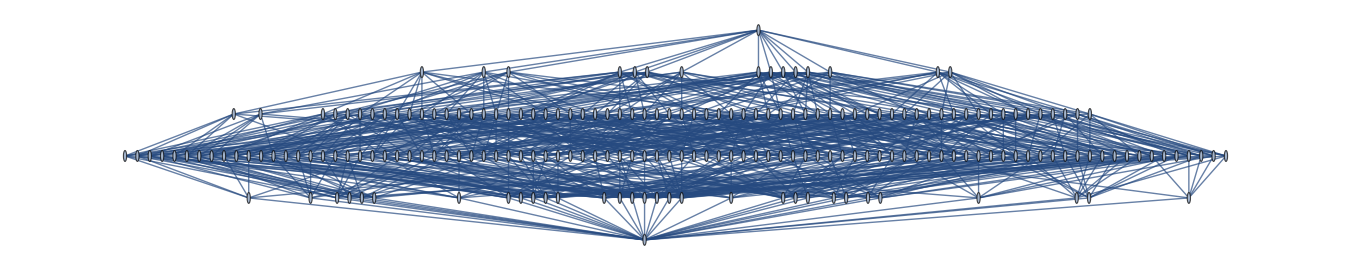

```mathematica
Graph[CoverRelations[setp6],GraphLayout->"LayeredDigraphEmbedding"]
```